```mathematica
Directory[]
```

C:\Users\Prajwal\Documents

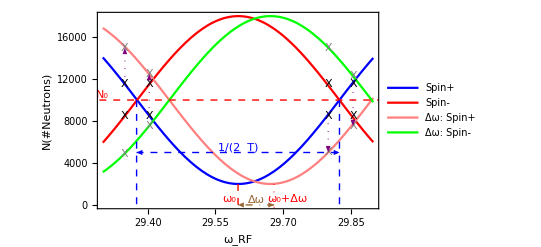

```mathematica
lineStyle={Thin,Red,Dashed};
lineStyle0={Thin,Red,Dotted};
line11=Line[{{29.2,10000},{30,10000}}];
line12=Line[{{29.6,2000},{29.6,-4200}}];
line012=Line[{{29.68,2000},{29.68,-4200}}];
lineStyle2={Thin,Blue,Dashed};
lineStyle3={Thick,Black};
lineStyle4={Thick,Gray};
lineStyle5={Thick,Purple,Dotted};
lineStyle6={Thick,Brown,DotDashed};
line21=Line[{{29.375,10000},{29.375,-8000}}];
line22=Line[{{29.825,10000},{29.825,-8000}}];
pt1[xx_]:=N[10000(1+0.8Cos[3-7xx])];
pt2[xx_]:=N[10000(1-0.8Cos[3-7xx])];
pt3[xx_]:=N[10000(1+0.8Cos[3.5-7xx])];
pt4[xx_]:=N[10000(1-0.8Cos[3.5-7xx])];
exp1=Plot[{pt1[xx],pt2[xx],pt3[xx],pt4[xx]},{xx,29.3,29.9},Frame->True,
Epilog->{
{Directive[lineStyle],line11,line12,Text[Style["N_0",FontSize->Large],{29.3,10500}],Text[Style["ω_0",FontSize->Large],{29.58,550}]},
{Directive[lineStyle0],line012,Text[Style["ω_0+Δω",FontSize->Large],{29.71,550}]},
{Directive[lineStyle2],line21,line22,{Arrowheads[{-.02,.02}],Arrow[{{29.375,5000},{29.825,5000}}]},Text[Style["1/(2  T)",FontSize->Large],{29.6,5500}]},
{Directive[lineStyle3],Text[Style["X",FontSize->Large],{29.349,11500}],Text[Style["X",FontSize->Large],{29.403,8500}],Text[Style["X",FontSize->Large],{29.8,8500}],Text[Style["X",FontSize->Large],{29.855,11500}],(**)Text[Style["X",FontSize->Large],{29.349,8500}],Text[Style["X",FontSize->Large],{29.403,11500}],Text[Style["X",FontSize->Large],{29.8,11500}],Text[Style["X",FontSize->Large],{29.855,8500}]},
{Directive[lineStyle4],Text[Style["X",FontSize->Large],{29.349,11500+3500}],Text[Style["X",FontSize->Large],{29.403,8500+4000}],Text[Style["X",FontSize->Large],{29.8,8500-3500}],Text[Style["X",FontSize->Large],{29.855,11500-4000}],(**)Text[Style["X",FontSize->Large],{29.349,8500-3600}],Text[Style["X",FontSize->Large],{29.403,11500-4000}],Text[Style["X",FontSize->Large],{29.8,11500+3500}],Text[Style["X",FontSize->Large],{29.855,8500+3800}]},
{Directive[lineStyle5],{Arrowheads[{0,0.02}],Arrow[{{29.349,11500},{29.349,11500+3500}}]},{Arrowheads[{0,0.02}],Arrow[{{29.403,8500},{29.403,8500+4000}}]},{Arrowheads[{0,0.02}],Arrow[{{29.8,8500},{29.8,8500-3500}}]},{Arrowheads[{0,0.02}],Arrow[{{29.855,11500},{29.855,11500-4000}}]}},
{Directive[lineStyle6],(*For Δω*){Arrowheads[{-.02,0.02}],Arrow[{{29.6,0},{29.68,0}}]},Text[Style["Δω",FontSize->Large],{29.64,500}]},
},
FrameLabel->{"ω_RF","N(#Neutrons)"},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},PlotLegends->{"Spin+","Spin-","Δω: Spin+","Δω: Spin-"},ImageSize->{1000},
PlotStyle->{Blue,Red,Pink,Green}]
```